## 3D Gauß

```mathematica
Assuming[{α>0, β>0, γ> 0},FullSimplify[FourierTransform[((2/π)^(3/4)*1/(√(α β γ))ⅇ^(-x^2/α^2-y^2/β^2-z^2/γ^2))^2,{x,y,z},{u,v,w}, FourierParameters->{1, -1}]]]
```

ⅇ^(1/8 (-u^2 α^2-v^2 β^2-w^2 γ^2))

## 1D parabola with heaviside

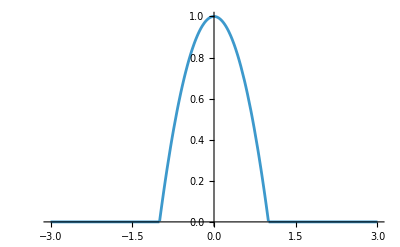

```mathematica
Plot[(-x^2+1)*HeavisideTheta[x+1]*HeavisideTheta[1-x],{x, -3, 3}]
```

```mathematica
FourierTransform[((-x^2+1)*HeavisideTheta[x+1]*HeavisideTheta[1-x])^2, x, k, FourierParameters->{1, -1}]
```

-(16 (3 k Cos[k]+(-3+k^2) Sin[k]))/k^5

## 3D parabola with heaviside

```mathematica
Manipulate[ContourPlot3D[(1 - x^2/a-y^2/b-z^2/c)*HeavisideTheta[1 - x^2/a-y^2/b-z^2/c]==.7, {x, -3,3},{y, -3,3}, {z, -3,3} ],{a, 1,3}, {b, 1, 3}, {c, 1, 3}]
```

```mathematica
FullSimplify[FourierTransform[(1 - x^2/a-y^2/b-z^2/c)*HeavisideTheta[1 - x^2/a-y^2/b-z^2/c],{x,y,z},{u,v,w}]]
```

(2 ⅈ √(2 π) DiracDelta[u] DiracDelta[v])/(c w^3)+(ⅈ √(2 π) DiracDelta[u] DiracDelta[v])/w+√2 π^(3/2) DiracDelta[u] DiracDelta[v] DiracDelta[w]+(ⅈ √(2 π) DiracDelta[v] DiracDelta''[u])/(a w)+(√2 π^(3/2) DiracDelta[v] DiracDelta[w] DiracDelta''[u])/a+(ⅈ √(2 π) DiracDelta[u] DiracDelta''[v])/(b w)+(√2 π^(3/2) DiracDelta[u] DiracDelta[w] DiracDelta''[v])/b